```mathematica
Quit[];
```

# C_g: Galaxy angular power spectrum

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/waco/Dropbox/Lensing/AngularProjectionPK

```mathematica
pkT=Import["test_00_pk.dat"];
pkT[[4]]
pkT=Drop[pkT,4]; (* Delete header (Class has 4 rows of header *)
pkl=Interpolation[Transpose[{pkT[[All,1]],pkT[[All,2]]}]]
kMin=pkT[[1,1]]
kMax=Last[pkT[[All,1]]]
```

{#,1:k,(h/Mpc),2:P,(Mpc/h)^3}

InterpolatingFunction[{{0.0000104206, 1.08688}}, <>]

0.0000104206

1.08688

## Background Cosmology

```mathematica
OmM=0.3;
H[z_]:=Sqrt[OmM (1+z)^3+(1-OmM)]  (*This is Hubble over H0 = H(z)/Subscript[H, 0]*)
H0=1/(2997.92458 );(*In h/Mpc*)
(* H0 = 100 h  km/s/Mpc ~ 1/3000  h/Mpc *)
```

### comoving distance χ (=chi)

χ(z) =  ∫_0^z dz'/(H(z'))

chiMin = 0. Mpc/h, chiMax = 7519.61 Mpc/h

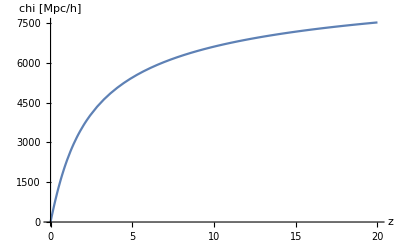

```mathematica
chiOfzIntegral[z_]:=NIntegrate[1/H[zp],{zp,0,z}]1/H0;(* χ(z) in units Mpc/h  *)

zMax=20;  (* zMax=20 is more than enough. We don't observe galaxies that far. *) 

(* Obtain χ(z)*)
chiOfzT=ParallelTable[{z,chiOfzIntegral[z]},{z,0,zMax,0.1}];
chiOfz=Interpolation[chiOfzT];
chiMax=Last[chiOfzT[[All,2]]];chiMin=chiOfzT[[1,2]];
Print["chiMin = ",chiMin, " Mpc/h", ", chiMax = ",chiMax, " Mpc/h"];
Plot[chiOfz[z],{z,0,20},AxesLabel->{"z","chi [Mpc/h]"}];
Print[%]
```

aOfchi:  a(χ) function:

amin = 0.047619, aMax = 1.

chiMin = 0. Mpc/h, chiMax = 7519.61 Mpc/h

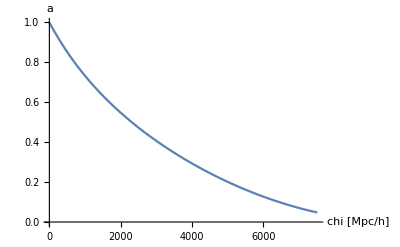

```mathematica
(*Invert to obtain z(χ) *)
zOfchiT=Table[{chiOfzT[[i,2]] ,chiOfzT[[i,1]]},{i,1,Length@chiOfzT}];
zOfchi=Interpolation[zOfchiT];

(*a(χ) = a(z(χ))*)
aOfchi[chi_]:=1/(1+zOfchi[chi]); 

aMin=aOfchi[chiMax];aMax=aOfchi[chiMin];
Print["aOfchi:  a(χ) function: "];
Print["amin = ",aMin, ", aMax = ",aMax];
Print["chiMin = ",chiMin, " Mpc/h", ", chiMax = ",chiMax, " Mpc/h"];
Plot[{aOfchi[x]},{x,0,chiMax},AxesLabel->{"chi [Mpc/h]","a"}];
Print[%]
```

## Linear growth function

Compute the linear growth function D+(eta), eta= log a(t)

We solve the linear equation

(d^2D)/dt^2 + 2 H dD/dt- 3/2 Ω_m(t)H^2(t) D = 0

with EdS initial conditions to pick up the growing solution. i.c. set at an early time D+ \propto a

Instead of use the time t  to integrate the diff equation, we use the variable eta= ln a(t).  Hence d / d t = H d / d eta    and we solve
D’’[eta] + (2 + H'[eta]/H[eta])D’[eta]  -  3/2 Ω_m [eta]D[eta] = 0

```mathematica
etaini=-6;
etafI=0.1;
Dplusi=Exp[etaini];
dDplusi=Exp[etaini];


f1[eta_]:=(2.-3./(2.(1.+(1-OmM)/OmM Exp[3.eta])));(*(2+H'[eta]/H[eta])*)
f2[eta_]:=3./(2.(1.+(1-OmM)/OmM Exp[3.eta]));(*3/2 Subscript[Ω, m] [eta]*)

sysDplus=NDSolve[{Df''[eta] +f1[eta]Df'[eta]-f2[eta] Df[eta]==0,Df'[etaini]==dDplusi,Df[etaini]==Dplusi},Df,{eta,etaini,etafI}];
DplusPre[eta_]:=Evaluate[Df[eta]/.sysDplus][[1]]; 
Dplusp[eta_]:=Evaluate[Df'[eta]/.sysDplus][[1]];

DplusPre[0] (* Not normalized to 1 nowadays *)
```

0.778985

```mathematica
etainiTable=etaini;
deltaLoga=0.1;
etafTable=0.1;
etaT=Table[etai,{etai,etainiTable,0,deltaLoga}];
DplusT=Table[{Exp[etai],DplusPre[etai]/DplusPre[0]},{etai,etainiTable,0,deltaLoga}];
Dplus=Interpolation[DplusT];
Plot[{Dplus[a]},{a,0.01,1}];
```

```mathematica
DplusEdS[a_]:=a Dplus[Exp[etaini]]/Exp[etaini];
Plot[{Dplus[a],DplusEdS[a]},{a,0.005,1},PlotLegends->{"D(a)","D(a) in EdS: \\propto a"},AxesLabel->{"a [Mpc/h]","a"}];
```

D_+(χ) = D_+(a(χ))

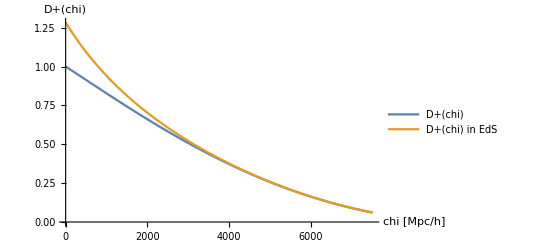

```mathematica
(*D_+(χ) = D_+(a(χ)) =*)
DplusOfchi[chi_]:=Dplus[aOfchi[chi]]
Plot[{DplusOfchi[chi],DplusEdS[aOfchi[chi]]},{chi,0,chiMax},PlotLegends->{"D+(chi)","D+(chi)  in EdS"},AxesLabel->{"chi [Mpc/h]","D+(chi)"}];
Print[%]
```

## W(χ) probability

W(χ) d χ   is the galaxy probability distribution in comoving distance. Normalized to 1  (∫_0^∞ W(χ')ⅆχ'  =1) 
I will use a window W function similar to the Gold Sample (https://arxiv.org/pdf/1809.01669.pdf)

```mathematica
zBin=1.0; (* this is the z at which the tomographic bin will be centered*)
chiBin=chiOfz[zBin];
Print["Tomographic Bin: z = ", zBin, ", Corresponds to chi = ", chiBin, " Mpc/ h"];
```

Tomographic Bin: z = 1., Corresponds to chi = 2312.68 Mpc/ h

1000.

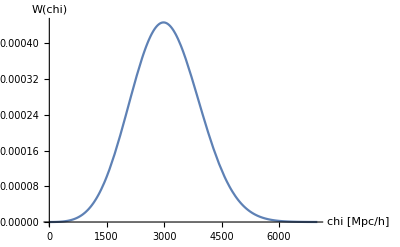

```mathematica
sigma2=1000^2;
Sqrt[sigma2 1.]
NormFac=chiBin ⅇ^(-chiBin^2/(2 sigma2)) sigma2+√(π/2) √sigma2 (chiBin^2+sigma2) (1+Erf[chiBin/(√2 √sigma2)]); 
W[x_]:=x^2 Exp[-(x-chiBin)^2/(2 sigma2)]/NormFac;

(*Integrate[W[x],{x,0,Infinity}]*)
Plot[W[chi],{chi,1,7000},PlotRange->All,AxesLabel->{"chi [Mpc/h]","W(chi)"}];
Print[%]
```

```mathematica
chiMax2=6500;
```

## Galaxy angular power spectrum:

C_g(l) = ∫_0^∞ ⅆχ  (W^2(χ))/χ^2P_g(k = (l+1/2)/χ,χ)

Table of ells, equal log intervals:

```mathematica
PddLinear[ell_,chi_]:= (DplusOfchi[chi])^2 pkl[(ell+1/2)/chi];
(*Pddloop[ell_,chi_]:= (DplusOfchi[chi])^4 (p22[(ell+1/2)/chi]+p13[(ell+1/2)/chi])*)
Pm[ell_,chi_]:=PddLinear[ell,chi](*+Pddloop[ell,chi]*) ;
```

BIAS: For simplicity, let’s take unbiased galaxies  b_1=1

```mathematica
b1[chi_]:=1;  (*this is unrealistic, one option can be 1+cte/D+  *)

(* Galaxy power spectrum*)
Pg[ell_,chi_]:= (b1[chi])^2 Pm[ell,chi];
```

## Integration

```mathematica
Nell=120;
ellini=3.;ellfin=2000;
delta=Log10[ellfin/ellini]/(Nell-1);
ellT=Table[10^(Log10[ellini]+delta(ii-1)),{ii,1,Nell}];
ellMin=First[ellT];
ellMax=Last[ellT];
Print["C_g(ell) will be computed from ellMin = ", ellMin, " to ellMax = ",ellMax," using ",Nell, " log-spaced points" ]

chimin[ell_]:=(ell+1/2)/kMax;
chimax[ell_]:=(ell+1/2)/kMin;
```

C_g(ell) will be computed from ellMin = 3. to ellMax = 2000. using 120 log-spaced points

Perform the integral

Cg(l) = ∫_0^∞ dχ  (W^2(χ))/χ^2P_g(k = (l+1/2)/χ,χ)

```mathematica
Print[chiMax,", ",chiMax2]
```

7519.61, 6500

chiMax2 is the χ where W(χ) is practically zero

```mathematica
power[ell_,chi_]:=Pg[ell,chi];
integrand[ell_,chi_]:=(W[chi]/chi)^2power[ell,chi];


CgT=Table[{0,0},{l,1,Length@ellT}];  (* Output table *)
Do[
ell=ellT[[l]];

chiminell=chimin[ell];
chimaxell=Min[chiMax,chimax[ell]];(* Max chi in integration *)



Nchi=100; (* Number of chi points in the integration.  *)
deltachi=(chimaxell-chiminell)/(Nchi-1);
(* Array of chi points for trapezoidal integration: *)
chiT=Table[chiminell+deltachi*(i-1),{i,1,Nchi}]; 

pg=0;pgB=0;
chiA=chiT[[1]];
pgA=integrand[ell,chiA];
Do[
chiB=chiT[[i]];
pgB=integrand[ell,chiB];
deltachi=chiB-chiA;
pg=pg+(pgA+pgB)/2  *deltachi;
chiA=chiB;
pgA=pgB;
,{i,2,Length@chiT}];

CgT[[l]]={ell,pg};
,{l,1,Length@ellT}]//AbsoluteTiming
```

{0.23627,Null}

### Plot

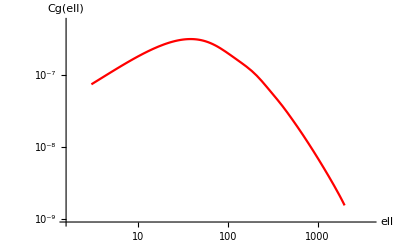

```mathematica
Cg=Interpolation[CgT];
p1=LogLogPlot[{Cg[ell]},{ell,3,2000},PlotStyle->{Black,Red},AxesLabel->{"ell","Cg(ell)"}]
LogLogPlot[{pkl[k]},{k,0.001,1}];
```

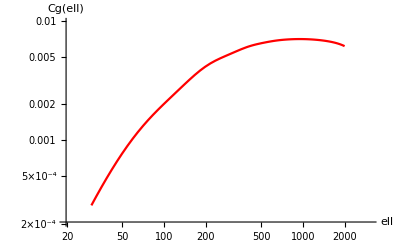

```mathematica
p1=LogLogPlot[{ell(ell+1)Cg[ell]},{ell,30,2000},PlotStyle->{Black,Red},AxesLabel->{"ell","Cg(ell)"}]
```